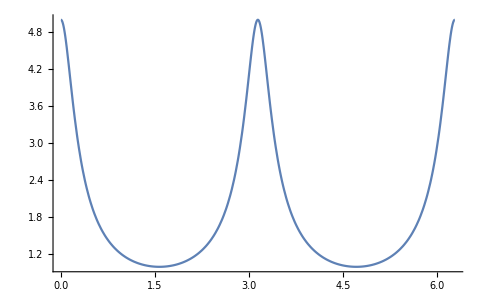

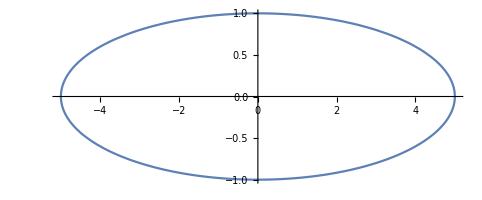

```mathematica
Subscript[λ, 1]=5.0;Subscript[λ, 2]=1.0;ϕ=0;
r=(Subscript[λ, 1] Subscript[λ, 2])/(√(Subscript[λ, 2]^2 Cos[θ+ϕ]^2+Subscript[λ, 1]^2 Sin[θ+ϕ]^2));
Plot[r,{θ,0,2Pi}]
PolarPlot[r,{θ,0,2Pi}]
```

```mathematica
0.5∫_0^(2Pi) r^2 ⅆθ
```

3.14159

```mathematica
∫_0^(2Pi) rⅆθ
```

12.0644

```mathematica
%/(2Pi)
```

1.92012

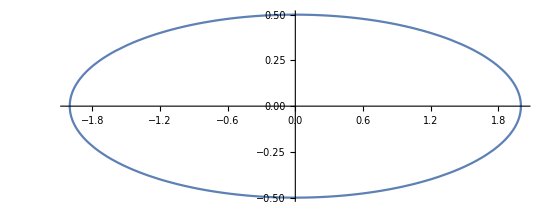

```mathematica
Subscript[λ, 1]=2.0;Subscript[λ, 2]=0.5;ϕ=0;
r=(Subscript[λ, 1] Subscript[λ, 2])/(√(Subscript[λ, 2]^2 Cos[θ+ϕ]^2+Subscript[λ, 1]^2 Sin[θ+ϕ]^2));
PolarPlot[r,{θ,0,2Pi}]
```

```mathematica
0.5∫_0^(2Pi) r^2 ⅆθ
```

3.14159

```mathematica
∫_0^(2Pi) rⅆθ
```

12.0644

```mathematica
%/(2Pi)
```

1.92012

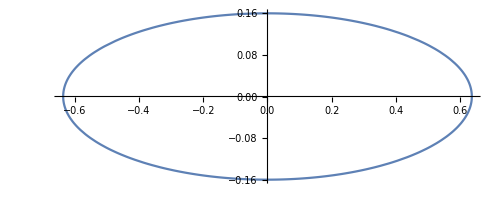

```mathematica
Subscript[λ, 1]=0.636619772368;Subscript[λ, 2]=0.159154943092;ϕ=0;
r=(Subscript[λ, 1] Subscript[λ, 2])/(√(Subscript[λ, 2]^2 Cos[θ+ϕ]^2+Subscript[λ, 1]^2 Sin[θ+ϕ]^2));
PolarPlot[r,{θ,0,2Pi}]
```

```mathematica
∫_0^(2Pi) rⅆθ
```

1.7833

```mathematica
∫_0^(2Pi) r^2 ⅆθ
```

7.90295

```mathematica
0.5∫_0^(2Pi) r^2 ⅆθ
```

3.95148

```mathematica
Clear[r]
r[θ_]=(Subscript[λ, 1] Subscript[λ, 2])/(√(Subscript[λ, 2]^2 Cos[θ+ϕ]^2+Subscript[λ, 1]^2 Sin[θ+ϕ]^2))
```

1.25779/(√(0.314449 Cos[θ]^2+5.03118 Sin[θ]^2))

```mathematica
r[45°]
r[0]
r[90°]
```

0.769352

2.24303

0.560757